## Arithmetic

### Complex Plane

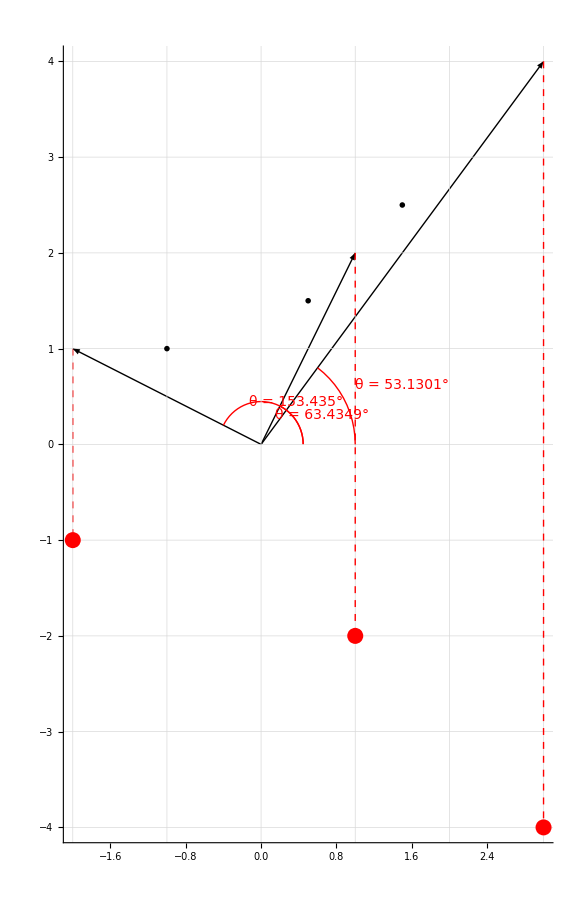

```mathematica
PlotComplexPlane[c_]:=Graphics[{
Arrow[{{0,0},{Re[#],Im[#]}}&/@c],
{Dashed,Red,PointSize->.02,Point[{Re[Conjugate[#]],Im[Conjugate[#]]}&/@c]},
Inset[MaTeX[Norm[#],Magnification->1.5],{.5*Re[#],.5*Im[#]+.5}]&/@c,
{Dashed,Red,Thick,Line[{{Re[#],Im[#]},{Re[#],-Im[#]}}&/@c]},
{Red,Thick,Circle[{0,0},Norm[#]/5,{0,Arg[#]}]&/@c},
Inset[Style["θ = "<>ToString[N[Arg[#]*180/π ]]<>"°",Red, Italic,14],{Cos[Arg[#]/2]+.6,Sin[Arg[#]/2+.2]}*Norm[#]/5]&/@c
}, Axes->True,ImageSize->Large,GridLines->{Range[-10,10], Range[-10,10]}]
PlotComplexPlane@{1+2I,3+4I,-2+1I}
```

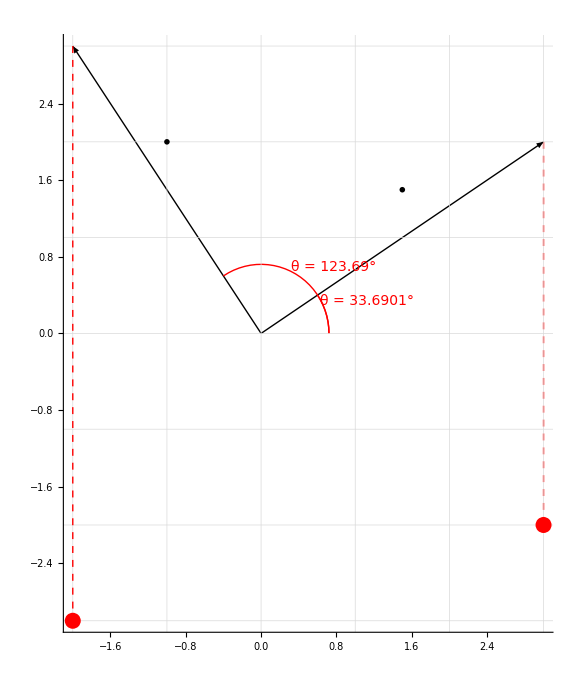

```mathematica
PlotComplexPlane@{3+2I,(3+2I)*I}
```

### Euler Formula

```mathematica
MaTeX[HoldForm[e^(I θ)== Cos[θ]+I Sin[θ]],Magnification->2]
```

-Graphics-

Around 1740, Euler

```mathematica
<<MaTeX`
```

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:\\Program Files\\MiKTeX 2.9\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs9.53.3\\bin\\gswin64c.exe"]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Program Files\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs9.53.3\bin\gswin64c.exe}

```mathematica
ResourceFunction["MaTeXInstall"][]
```

```mathematica
MaTeX`Information`$Version
```

1.7.8 (October 21, 2020)

```mathematica
f[x_]:=Table[x^n/(n!),{n,0,10}]
```

```mathematica
5!
```

120

```mathematica
f[I a]
```

{1,ⅈ a,-a^2/2,-(ⅈ a^3)/6,a^4/24,(ⅈ a^5)/120,-a^6/720,-(ⅈ a^7)/5040,a^8/40320,(ⅈ a^9)/362880,-a^10/3628800}

```mathematica
Partition[f[I a], 2,2]//Transpose
```

{{1,-a^2/2,a^4/24,-a^6/720,a^8/40320},{ⅈ a,-(ⅈ a^3)/6,(ⅈ a^5)/120,-(ⅈ a^7)/5040,(ⅈ a^9)/362880}}

```mathematica
CS=Total/@%
```

{1-a^2/2+a^4/24-a^6/720+a^8/40320,ⅈ a-(ⅈ a^3)/6+(ⅈ a^5)/120-(ⅈ a^7)/5040+(ⅈ a^9)/362880}

```mathematica
D[CS[[1]],a]
D[CS[[2]]/I,a]//Simplify
```

-a+a^3/6-a^5/120+a^7/5040

1-a^2/2+a^4/24-a^6/720+a^8/40320